```mathematica
uval=DSolveValue[{D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==0,u[x,0]==0,u[x,2]==10,u[0,y]==0,u[4,y]==0},u,{x,0,4},{y,0,2}]
```

Function[{x,y},-(20 (-1+(-1)^K[1]) Csch[1/2 π K[1]] Sin[1/4 π x K[1]] Sinh[1/4 π y K[1]])/(π K[1])K[1]1∞]

InterpolatingFunction[…]

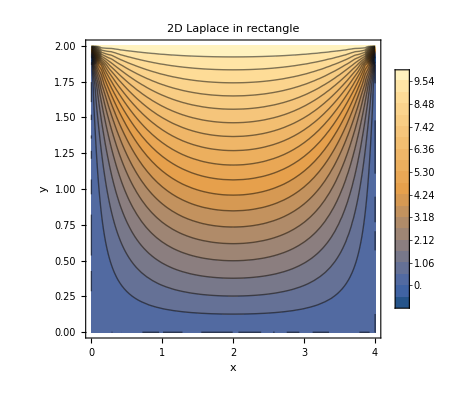

```mathematica
uval=NDSolveValue[{D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==0,u[x,0]==0,u[x,2]==10,u[0,y]==0,u[4,y]==0},u,{x,0,4},{y,0,2}]

ContourPlot[uval[x,y],{x,0,4},{y,0,2},FrameLabel->{"x","y"},PlotLabel->"2D Laplace in rectangle",PlotLegends->Automatic, Contours->20]
```

```mathematica
u[x_,y_,n_]:= Sum[(20 (1-(-1)^i)  (ⅇ^((-π i)/4 y)-ⅇ^((π i)/4 y))Sin[1/4 π x i])/((ⅇ^((-π i)/2)-ⅇ^((π i)/2))π i),{i, 1, n}]
```

```mathematica
u[1,1,100]//N
```

3.64057

# Сравнение с точным решением

## Сетка 0.01

```mathematica
X = Import["/home/san/Code/2d_Laplace_eq_FEM/domains/domain_2/mesh001/mesh_nodes.csv", {"Data", All, 1}];
Y = Import["/home/san/Code/2d_Laplace_eq_FEM/domains/domain_2/mesh001/mesh_nodes.csv", {"Data", All, 2}];
Z = Import["/home/san/Code/2d_Laplace_eq_FEM/output/domain_2_extra/mesh001/Test_domain_2_rectangle_dirichlet_only_solution.csv", {"Data", All, 1}];
X=Delete[X,1];
Y=Delete[Y,1];
Z=Delete[Z,1];
```

```mathematica
Err = {};
For[k = 1, k < Length@Z, ++k,AppendTo[Err,Abs[ Z[[k]]-u[X[[k]],Y[[k]],200 ]]]]
```

```mathematica
Mean[Err]
```

0.156825

## Сетка 0.001

```mathematica
X = Import["/home/san/Code/2d_Laplace_eq_FEM/domains/domain_2/mesh0001/mesh_nodes.csv", {"Data", All, 1}];
Y = Import["/home/san/Code/2d_Laplace_eq_FEM/domains/domain_2/mesh0001/mesh_nodes.csv", {"Data", All, 2}];
Z = Import["/home/san/Code/2d_Laplace_eq_FEM/output/domain_2_extra/mesh0001/Test_domain_2_rectangle_dirichlet_only_0001_solution.csv", {"Data", All, 1}];
X=Delete[X,1];
Y=Delete[Y,1];
Z=Delete[Z,1];
```

```mathematica
Err = {};
For[k = 1, k < Length@Z, ++k,AppendTo[Err,Abs[ Z[[k]]-u[X[[k]],Y[[k]],200 ]]]]
```

```mathematica
Mean[Err]
```

0.0625756